# CriticalPlot 整理版

## 1. 初始化与依赖加载

```mathematica
SetDirectory[NotebookDirectory[]];
Get["academic.m"];
Needs["MaTeX`"];
```

## 2. 数据导入与 Binder 累积量作图

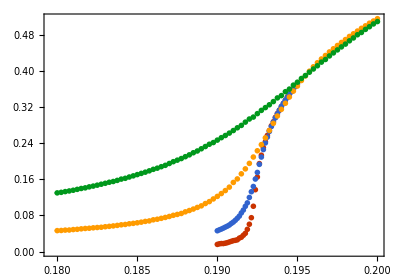

```mathematica
(* Binder cumulant 曲线，不同 L 的数据 *)
binderPlot=ListPlot[
  {
     {#1,Around[#2,#3]} & @@@ Import["scan_3D_L64_n10000.csv"][[2 ;; -1,{1,2,3}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_3D_L32_n80000.csv"][[2 ;; -1,{1,2,3}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_3D_L16_n160000.csv"][[2 ;; -1,{1,2,3}]],{#1,Around[#2,#3]} & @@@ Import["scan_3D_L8_n320000.csv"][[2 ;; -1,{1,2,3}]]
  },
  IntervalMarkers->"Fences",
  IntervalMarkersStyle-><|"FenceWidth"->0.00015|>,
  FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"\\kappa","\\langle|\\phi| \\rangle"}),
  PlotLegends->Placed[
    LineLegend[
      (MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"L=64","L=32","L=16","L=8"}),
      LegendMarkerSize->{40,12},
      LegendLayout->{"Column",1}
    ],
    Scaled[{0.75,0.3}]
  ]
];

binderPlot
```

```mathematica
Export["orderparameter_3d_wolff_fahmc.pdf",binderPlot]
```

orderparameter_2d_wolff_fahmc.pdf

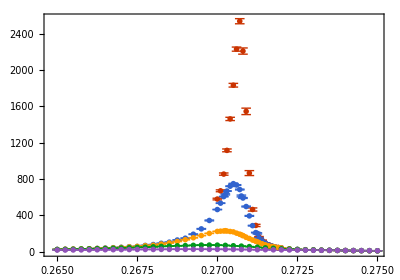

```mathematica
(* 磁化率曲线，不同 L 的数据 *)
chiPlot=ListPlot[
  {
    {#1,Around[#2,#3]} & @@@ Import["scan_L256_n10000.csv"][[2 ;; -1,{1,4,5}]],
    SortBy[DeleteDuplicatesBy[({#1,Around[#2,#3]} & @@@ Import["scan_L128_n50000.csv"][[2 ;; -1,{1,4,5}]])~Join~({#1,Around[#2,#3]} & @@@ Import["scan_L128_n10000_wide.csv"][[2 ;; -1,{1,4,5}]]),First],First],
    SortBy[DeleteDuplicatesBy[({#1,Around[#2,#3]} & @@@ Import["scan_L64_n50000.csv"][[2 ;; -1,{1,4,5}]])~Join~({#1,Around[#2,#3]} & @@@ Import["scan_L64_n20000_wide.csv"][[2 ;; -1,{1,4,5}]]),First],First],
    {#1,Around[#2,#3]} & @@@ Import["scan_L32_n20000.csv"][[2 ;; -1,{1,4,5}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_L16_n20000.csv"][[2 ;; -1,{1,4,5}]]
  },PlotRange->All,
  IntervalMarkers->"Fences",
  IntervalMarkersStyle-><|"FenceWidth"->0.00015|>,
  FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"\\kappa","\\chi"}),
  PlotLegends->Placed[
    LineLegend[
      (MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"L=256","L=128","L=64","L=32","L=16"}),
      LegendMarkerSize->{40,12},
      LegendLayout->{"Column",1}
    ],
    Scaled[{0.75,0.7}]
  ]
];
chiPlot
```

```mathematica
Export["chi_2d_wolff_fahmc_1.pdf",chiPlot]
```

chi_2d_wolff_fahmc_1.pdf

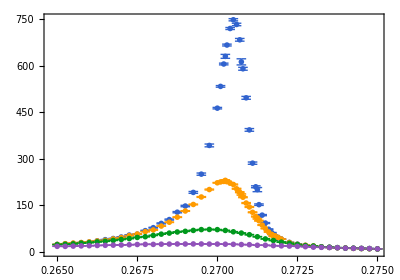

```mathematica
(* 磁化率曲线，不同 L 的数据 *)
chiPlot=ListPlot[
  {{ⅈ,ⅈ},
    
    SortBy[DeleteDuplicatesBy[({#1,Around[#2,#3]} & @@@ Import["scan_L128_n50000.csv"][[2 ;; -1,{1,4,5}]])~Join~({#1,Around[#2,#3]} & @@@ Import["scan_L128_n10000_wide.csv"][[2 ;; -1,{1,4,5}]]),First],First],
    SortBy[DeleteDuplicatesBy[({#1,Around[#2,#3]} & @@@ Import["scan_L64_n50000.csv"][[2 ;; -1,{1,4,5}]])~Join~({#1,Around[#2,#3]} & @@@ Import["scan_L64_n20000_wide.csv"][[2 ;; -1,{1,4,5}]]),First],First],
    {#1,Around[#2,#3]} & @@@ Import["scan_L32_n20000.csv"][[2 ;; -1,{1,4,5}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_L16_n20000.csv"][[2 ;; -1,{1,4,5}]]
  },PlotRange->All,
  IntervalMarkers->"Fences",
  IntervalMarkersStyle-><|"FenceWidth"->0.00015|>,
  FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"\\kappa","\\chi"}),
  PlotLegends->Placed[
    LineLegend[
      {None}~Join~(MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"L=128","L=64","L=32","L=16"}),
      LegendMarkerSize->{40,12},
      LegendLayout->{"Column",1}
    ],
    Scaled[{0.75,0.7}]
  ]
];
chiPlot
```

```mathematica
Export["chi_2d_wolff_fahmc_2.pdf",chiPlot]
```

chi_2d_wolff_fahmc_2.pdf

## 3. 插值函数的生成

```mathematica
(* 各个系统尺寸对应的插值函数 *)
f1=Interpolation[
  {#1,#2} & @@@ Import["scan_L256_n10000.csv"][[2 ;; -1,{1,6,7}]],
  Method->"Spline"
];
f2=Interpolation[
  {#1,#2} & @@@ Import["scan_L128_n50000.csv"][[2 ;; -1,{1,6,7}]],
  Method->"Spline"
];
f3=Interpolation[
  {#1,#2} & @@@ Import["scan_L64_n50000.csv"][[2 ;; -1,{1,6,7}]],
  Method->"Spline",InterpolationOrder->2
];
f4=Interpolation[
  {#1,#2} & @@@ Import["scan_L32_n100000.csv"][[2 ;; -1,{1,6,7}]],
  Method->"Spline"
];
f5=Interpolation[
  {#1,#2} & @@@ Import["scan_L16_n20000.csv"][[2 ;; -1,{1,6,7}]],
  Method->"Spline"
];
```

## 4. 交点查找与拟合

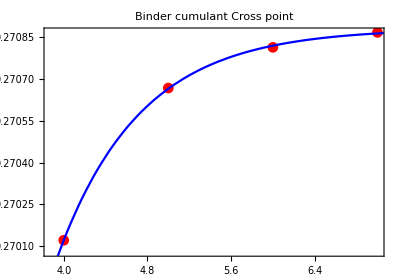

```mathematica
(* 查找不同 L 曲线的交点 *)
crossPoints=Table[
  x /. FindRoot[
    {f1,f2,f3,f4,f5}[[i]][x]=={f1,f2,f3,f4,f5}[[i+1]][x],
    {x,0.2705}
  ],
  {i,1,4}
];

(* 交点数据整理 *)
crossData=Transpose[{{7,6,5,4},crossPoints}];

(* 指数型拟合（可根据实际需求调整模型） *)
fitModel=a*Exp[b*x]+c;
fitParams=FindFit[crossData,fitModel,{{a,-1},{b,-1},{c,0.2709}},x];
fitFun[x_]=fitModel /. fitParams;

(* 可视化交点及拟合曲线 *)
Show[
  ListPlot[N[{2^#1,#2}&@@@crossData],PlotStyle->Red,PlotMarkers->Automatic,PlotLabel->"Binder cumulant Cross point",ScalingFunctions->{"Log2",Automatic},FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"L","\\kappa"})],
  Plot[fitFun[Log[2,x]],{x,2^3,2^10},PlotStyle->Blue,ScalingFunctions->{"Log2",Automatic}]
]
```

```mathematica
Export["bindercross_2d_wolff_fahmc.pdf",%]
```

bindercross_2d_wolff_fahmc.pdf

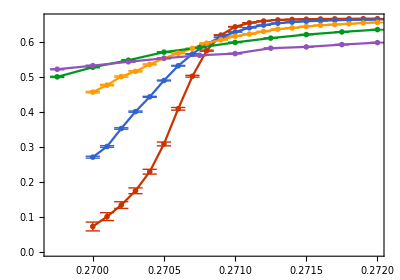

```mathematica
(* Binder 累积量曲线，不同 L 的数据 *)
binderPlot=ListLinePlot[
  {
    {#1,Around[#2,#3]} & @@@ Import["scan_L256_n10000.csv"][[2 ;; -1,{1,6,7}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_L128_n50000.csv"][[2 ;; -1,{1,6,7}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_L64_n20000.csv"][[2 ;; -1,{1,6,7}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_L32_n20000.csv"][[21 ;; -13,{1,6,7}]],
    {#1,Around[#2,#3]} & @@@ Import["scan_L16_n20000.csv"][[21 ;; -13,{1,6,7}]]
  },
  IntervalMarkers->"Fences",
  IntervalMarkersStyle-><|"FenceWidth"->0.00005|>,
  FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"\\kappa","\\mathrm{Binder}~U_L"}),
  PlotLegends->Placed[
    LineLegend[
      (MaTeX[#,ContentPadding->False,FontSize->15] & /@ {"L=256","L=128","L=64","L=32","L=16"}),
      LegendMarkerSize->{40,12},
      LegendLayout->{"Column",1}
    ],
    Scaled[{0.75,0.3}]
  ]
];
binderPlot
```

```mathematica
Export["binder_2d_wolff_fahmc.pdf",binderPlot]
```

binder_2d_wolff_fahmc.pdf

## Propagator

```mathematica
SetDirectory["..\\correlation_k=0.28"]
```

E:\DM\2Dphi4\correlation_k=0.28

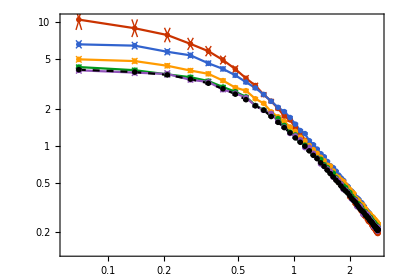

```mathematica
ListLinePlot[{{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=0049.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=00_steps=0400.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=01.dat"],*)(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=99.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=0099.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=0999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=1499.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=1999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_HMC_28_0.022.dat"]}[[All,2;;-2,All]],IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->0.035|>
,ScalingFunctions->{"Log","Log"},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Black,Dashed]},PlotLegends->Placed[LineLegend[(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"50~ \\mathrm{Epoches}","100~ \\mathrm{Epoches}","1000~ \\mathrm{Epoches}","1500~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}","\\mathrm{HMC}"}),LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.5,0.3}]],FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"|k|","G(|k|)"})]
```

```mathematica
Export["prop_k=0.28_log_log.pdf",%]
```

prop_k=0.28_log_log.pdf

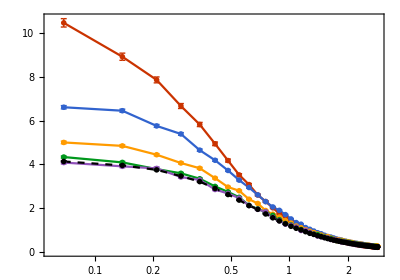

```mathematica
ListLinePlot[{{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=0049.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=00_steps=0400.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=01.dat"],*)(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=99.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=0099.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=0999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=1499.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_28_0.022_epoch=1999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_HMC_28_0.022.dat"]}[[All,2;;-2,All]],IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->0.035|>
,ScalingFunctions->{"Log",Automatic},PlotRange->All,PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Black,Dashed]},PlotLegends->Placed[LineLegend[(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"50~ \\mathrm{Epoches}","100~ \\mathrm{Epoches}","1000~ \\mathrm{Epoches}","1500~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}","\\mathrm{HMC}"}),LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.75,0.7}]],FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"|k|","G(|k|)"})]
```

```mathematica
Export["prop_k=0.28_log.pdf",%]
```

prop_k=0.28_log.pdf

```mathematica
SetDirectory["..\\correlation_k=0.26"]
```

E:\DM\2Dphi4\correlation_k=0.26

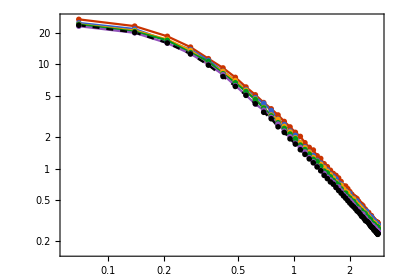

```mathematica
ListLinePlot[{{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=0099.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=00_steps=0400.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=01.dat"],*)(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=99.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1099.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1199.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1299.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1499.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_HMC_26_0.022.dat"]}[[All,2;;-2,All]](*,IntervalMarkers->"Fences"*),IntervalMarkersStyle-><|"FenceWidth"->0.035|>
,ScalingFunctions->{"Log","Log"},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Black,Dashed]},PlotLegends->Placed[LineLegend[(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"50~ \\mathrm{Epoches}","100~ \\mathrm{Epoches}","1000~ \\mathrm{Epoches}","1500~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}","\\mathrm{HMC}"}),LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.5,0.3}]],FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"|k|","G(|k|)"})]
```

```mathematica
Export["prop_k=0.26_log_log.pdf",%]
```

prop_k=0.26_log_log.pdf

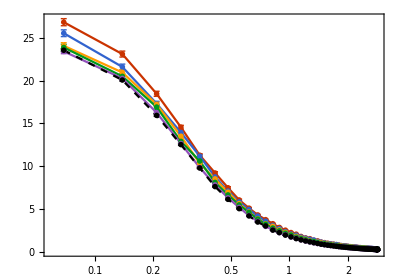

```mathematica
ListLinePlot[{{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=0099.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=00_steps=0400.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=01.dat"],*)(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=99.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=0999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1199.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1299.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=4999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_HMC_26_0.022.dat"]}[[All,2;;-2,All]],IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->0.035|>
,ScalingFunctions->{"Log",Automatic},PlotRange->All,PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Black,Dashed]},PlotLegends->Placed[LineLegend[(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"100~ \\mathrm{Epoches}","100~ \\mathrm{Epoches}","1000~ \\mathrm{Epoches}","1500~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}","\\mathrm{HMC}"}),LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.75,0.7}]],FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"|k|","G(|k|)"})]
```

```mathematica
Export["prop_k=0.26_log.pdf",%]
```

prop_k=0.26_log.pdf

```mathematica
SetDirectory["..\\correlation_k=0.2705"]
```

E:\DM\2Dphi4\correlation_k=0.2705

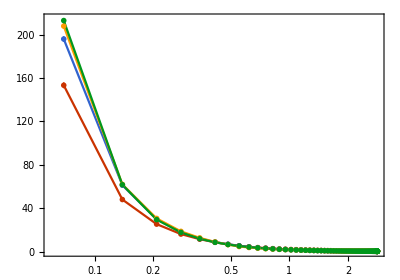

```mathematica
ListLinePlot[{{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_2705_0.022_epoch=0199.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=00_steps=0400.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=01.dat"],*)(*{#1,Around[#2,#3]}&@@@Import["G_k_32_jk_DM_512_2_epoch=99.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_2705_0.022_epoch=1999.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_2705_0.022_epoch=9999.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1299.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1499.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_HMC_2705_0.022.dat"]}[[All,2;;-2,All]](*,IntervalMarkers->"Fences"*),IntervalMarkersStyle-><|"FenceWidth"->0.035|>
,ScalingFunctions->{"Log",Automatic},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Black,Dashed]},PlotLegends->Placed[LineLegend[(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"200~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}","10000~ \\mathrm{Epoches}",(*"1500~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}",*)"\\mathrm{HMC}"}),LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.7,0.4}]],FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"|k|","G(|k|)"}),PlotRange->All]
```

```mathematica
Export["prop_k=0.2705_log.pdf",%]
```

```mathematica
Show[ListLinePlot[{{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_2705_0.022_epoch=9999.dat"],(*{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1299.dat"],{#1,Around[#2,#3]}&@@@Import["G_k_128_boot_DM_26_0.022_epoch=1499.dat"],*){#1,Around[#2,#3]}&@@@Import["G_k_128_boot_HMC_2705_0.022.dat"]}[[All,2;;-2,All]](*,IntervalMarkers->"Fences"*),IntervalMarkersStyle-><|"FenceWidth"->0.035|>
,ScalingFunctions->{"Log","Log"},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Directive[Black,Dashed]},PlotLegends->Placed[LineLegend[(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"\\mathrm{DM}",(*"1500~ \\mathrm{Epoches}","2000~ \\mathrm{Epoches}",*)"\\mathrm{HMC}"}),LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.3,0.4}]],FrameLabel->(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"|k|","G(|k|)"}),PlotRange->All],Plot[{ⅈ,ⅈ,1.94/p^(2-0.25),1.94/p^2},{p,0.05,100},ScalingFunctions->{"Log","Log"},PlotLegends->Placed[LineLegend[Flatten[{None,None,(MaTeX[#,ContentPadding->False,FontSize->15]&/@{"\\propto \\frac{1}{p^{2-\\eta}}","\\propto \\frac{1}{p^{2}}"})}],LegendMarkerSize->{40,12},LegendLayout->{"Column",1}],Scaled[{0.3,0.4}]]]]
```

-Graphics-

```mathematica
Export["prop_k=0.2705_log_log.pdf",%]
```

prop_k=0.2705_log.pdf